## Spectra Plots

```mathematica
ContextRemove["UWTools`"]
```

```mathematica
<<UWTools`
<<ChemTools`Wavefunctions`
<<ChemTools`Spectroscopy`
<<ChemTools`DataStructures`
WavefunctionsObject;
GridFunctionObject;
CoordinateGridObject;
```

```mathematica
h5Dir=FileNameJoin@{$UWDirectory,"Research", "H5+" };
```

## Notes

#### Notes for the morning since it’s 4:30 AM

Things look somewhat off, seemingly because of the new potential I calculated. So that it’d be done before too long I actually went somewhat *less* refined than the scan I had before, but over a larger range.

Since stuff went pear-shaped or whatever I’m running a new scan over the same larger range, but more refined. I’m including an interpolation to expand things, too. Hopefully these factors get rid of the shift in the frequencies.

In terms of *where* these new shifts are coming from it is essentially 100% the averaged potential energy surface. For the equilibrium H2 position in the shared proton fundamental frequency is raised by about 20 wavenumbers but the potential from averaging over the outer H2s gives results a difference of 200 wavenumbers. The potentials are qualitatively quite similar, but zooming in on a region we can see the differences:

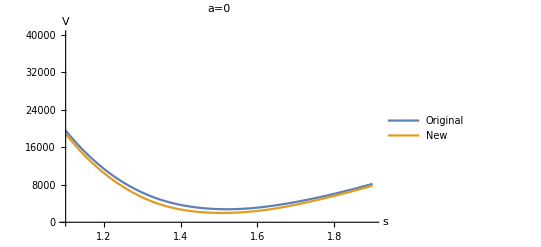

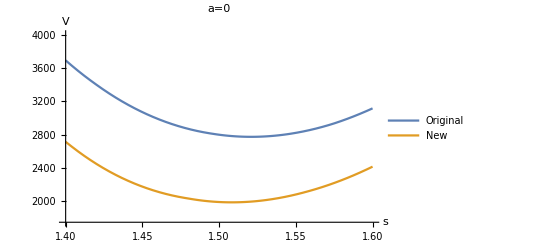

I haven’t looked at the higher excitations, but the working assumption is that the same trend will continue.

## Base Data

### H5

#### Bowtie

```mathematica
h5SpecParts=
Import[FileNameJoin@{h5Dir,"results", "H5HighRes", "Spectra.mx"}];
h5Spec=Join@@h5SpecParts[[;;3]];
```

```mathematica
h5LowResParts=
Import[FileNameJoin@{h5Dir, "results", "H5", "Spectra.mx"}];
h5LowResSpec=Join@@h5LowResParts[[;;3]];
```

```mathematica
h5HighResParts=
Import[FileNameJoin@{h5Dir, "results", "H5ExtraHighRes", "Spectra.mx"}];
h5HighResSpec=Join@@h5HighResParts[[;;3]];
```

#### Parallel

```mathematica
h5ParallelLowResSpecParts=
Import[FileNameJoin@{h5Dir, "results", "H5Parallel", "Spectra.mx"}];
h5ParallelLowResSpec=Join@@h5ParallelLowResSpecParts[[;;3]];
```

```mathematica
h5ParallelSpecParts=
Import[FileNameJoin@{h5Dir, "results", "H5ParallelHighRes", "Spectra.mx"}];
h5ParallelSpec=Join@@h5ParallelSpecParts[[;;3]];
```

### D5

#### Bowtie

```mathematica
d5SpecParts=
Import[FileNameJoin@{h5Dir, "results", "D5HighRes", "Spectra.mx"}];
d5Spec=Join@@d5SpecParts[[;;3]];
```

```mathematica
d5LowResSpecParts=
Import[FileNameJoin@{h5Dir, "results", "D5", "Spectra.mx"}];
d5LowResSpec=Join@@d5SpecParts[[;;3]];
```

#### Parallel

```mathematica
d5ParallelSpecParts=Import[FileNameJoin@{h5Dir, "results", "D5Parallel", "Spectra.mx"}];
d5ParallelSpec=Join@@d5ParallelSpecParts[[;;3]];
```

### Old

##### H5

```mathematica
h5OldSpecParts=
Import[FileNameJoin@{h5Dir,"results", "H5OldOriginal", "$Spectra.mx"}];
h5OldSpec=Join@@h5OldSpecParts[[;;3]];
```

##### D5

```mathematica
d5OldSpecParts=
Import[FileNameJoin@{h5Dir, "results", "D5Old", "$Spectra.mx"}];
d5OldSpec=Join@@d5OldSpecParts[[;;3]];
```

## Specs

### H5

```mathematica
h5LowResParts[[1]]@"Frequencies"
```

#### Lower Res

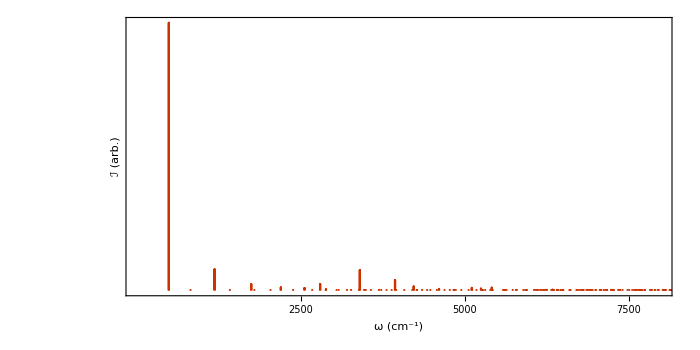

```mathematica
spectrumPlot[h5LowResSpec, PlotRange->{{0, 8000}, {0, 1}}]
```

##### Zoom 1

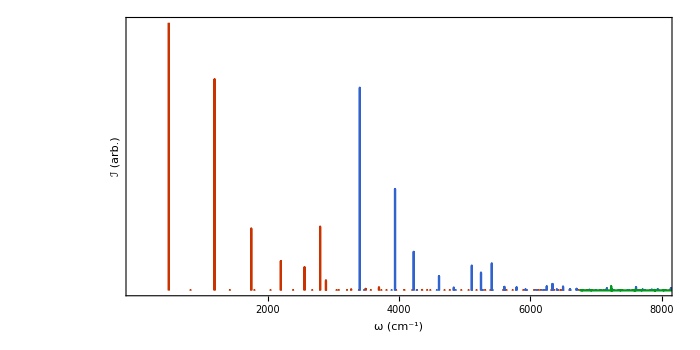

```mathematica
spectrumPlot[h5LowResParts[[;;3]], PlotRange-> {{0, 8000}, {0, .1}}]
```

#### Bowtie

##### Full

```mathematica
spectrumPlot[h5SpecParts[[;;3]], PlotRange->{{0, 8000}, {0, 1}}]
```

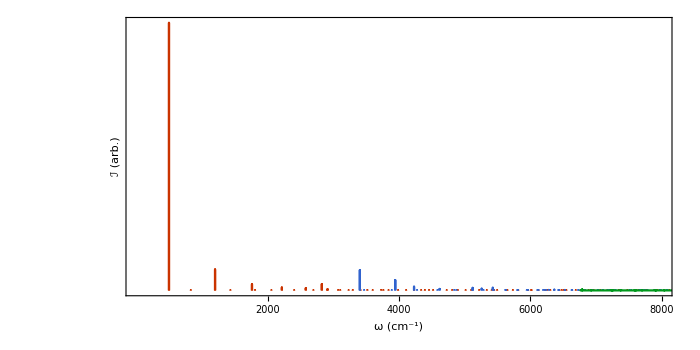

```mathematica
s
```

##### Zoom 1

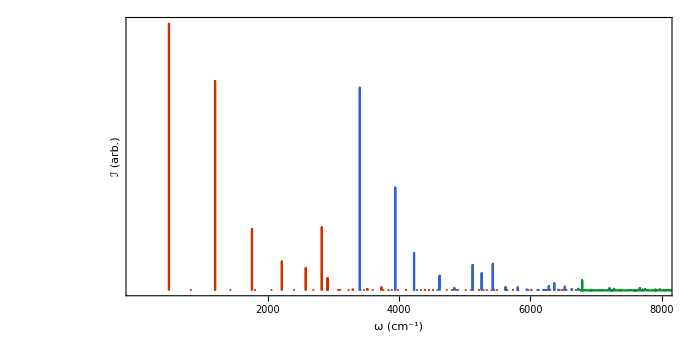

```mathematica
spectrumPlot[h5SpecParts[[;;3]], PlotRange-> {{0, 8000}, {0, .1}}]
```

##### Zoom 2

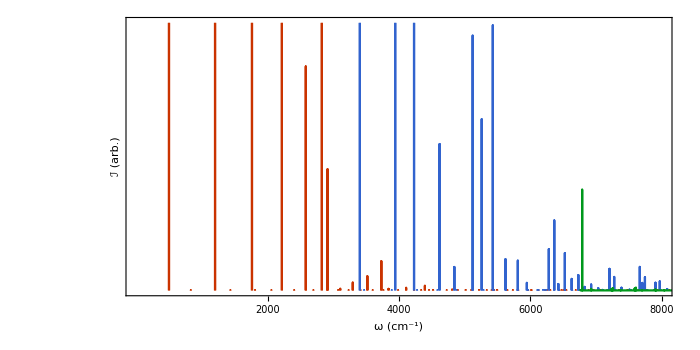

```mathematica
spectrumPlot[h5SpecParts[[;;3]], PlotRange-> {{0, 8000}, {0, .01}}]
```

#### Parallel

##### Full

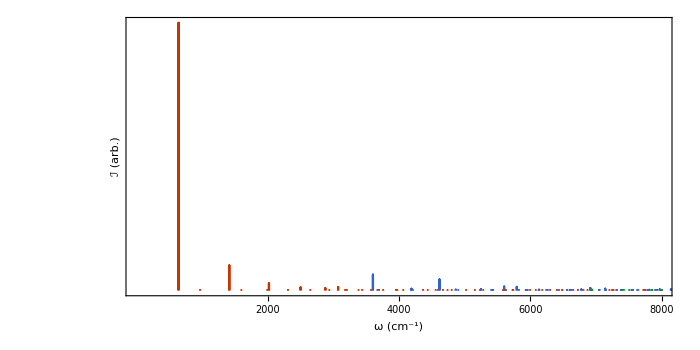

```mathematica
spectrumPlot[h5ParallelSpecParts[[;;3]], PlotRange->{{0, 8000}, {0, 1}}]
```

##### Zoom 1

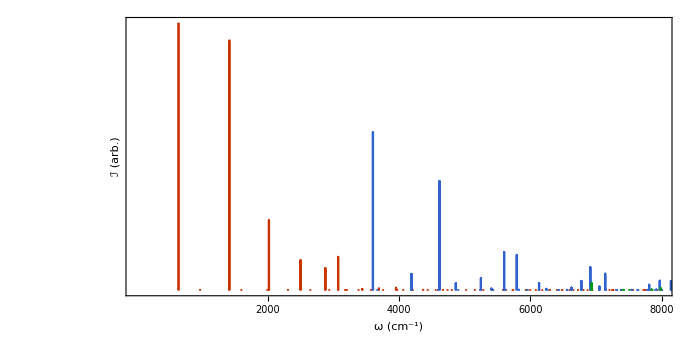

```mathematica
spectrumPlot[h5ParallelSpecParts[[;;3]], PlotRange-> {{0, 8000}, {0, .1}}]
```

##### Zoom 2

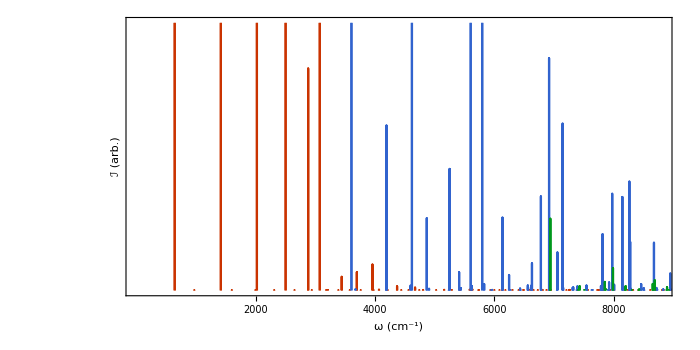

```mathematica
spectrumPlot[h5ParallelSpecParts[[;;3]], PlotRange-> {{0, 8800}, {0, .01}}]
```

### D5

#### Bowtie

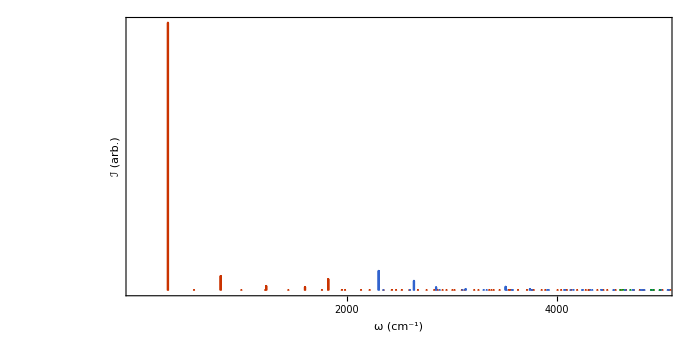

```mathematica
spectrumPlot[d5SpecParts[[;;3]], PlotRange-> {{0, 5000}, {0, 1}}]
```

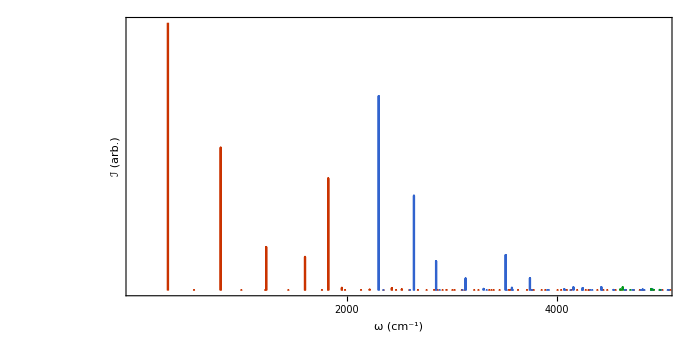

```mathematica
spectrumPlot[d5SpecParts[[;;3]], PlotRange-> {{0, 5000}, {0, .1}}]
```

#### Parallel

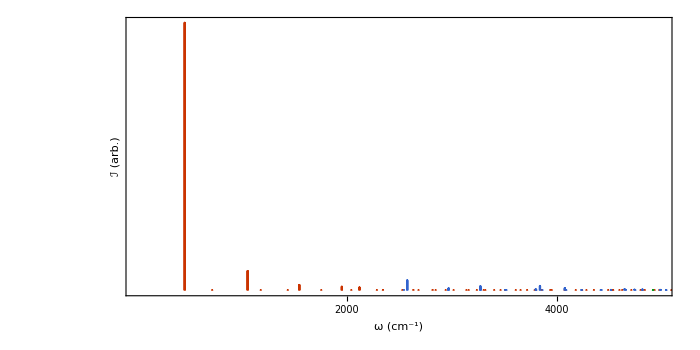

```mathematica
spectrumPlot[d5ParallelSpecParts[[;;3]], PlotRange-> {{0, 5000}, {0, 1}}]
```

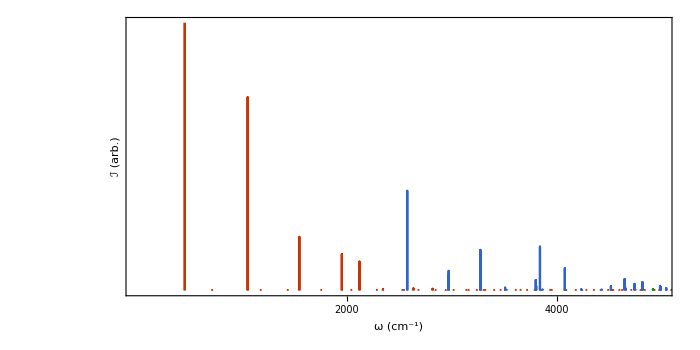

```mathematica
spectrumPlot[d5ParallelSpecParts[[;;3]], PlotRange-> {{0, 5000}, {0, .1}}]
```

### Comparisons of Spectra I Have

#### H Bowtie / Parallel

#### D Bowtie / Parallel

#### Old H / New H (something’s weird) / All D

### Comparison to Expt

```mathematica
localFig[name_]:=
FileNameJoin@{h5Dir, "figures", name}
```

#### Load Expt. Data

```mathematica
digitData=;
h5Higher=;
spectra=
ChemSpectrum/@
MapThread[
Transpose[{1, #3}*Transpose[MovingAverage[#, #2]]]&,
{
Append[digitData[[{2, 1, 3}]], h5Higher],
{125, 50, 100, 10},
{.08, .1, .01, .01}
}
];
spec1Shift=
940-MaximalBy[spectra[[1]]@"Points", Last][[1, 1]];
spectra[[1]]=
spectra[[1]]@"Shift"[spec1Shift];
spec2Shift=
3520-MaximalBy[spectra[[2]]@"Points", Last][[1, 1]];
spectra[[2]]=
spectra[[2]]@"Shift"[spec2Shift];
spec3Shift=
6684-MaximalBy[spectra[[3]]@"Window"[{5000, All}, {.005, All}]@"Points", Last][[1, 1]];
spectra[[3]]=
spectra[[3]]@"Shift"[spec3Shift];
spec4Shift=
6684-MaximalBy[spectra[[4]]@"Points", Last][[1, 1]];
spectra[[4]]=
spectra[[4]]@"Shift"[spec4Shift];
joinedSpec=Join@@spectra;
```

```mathematica
d5Digit=;
d5Expt=
ChemSpectrum@
Transpose[{1, .1}*Transpose[MovingAverage[d5Digit, 50]]];
```

```mathematica
zhouSpec=ChemSpectrum[…];
```

#### Compare with scales

##### makeCompPlot

```mathematica
makeCompPlot[specs_, spectra_]:=
MapIndexed[
Show[
spectrumPlot[
#, 
PlotStyle->Directive[ColorData[97][3], Opacity[.5]],
Filling->Axis,
FillingStyle->
Opacity[.5],
AspectRatio->.33,
PlotRange->{All, {-.0150/(10^(#2[[1]]*2/3)), All}}
],
spectrumPlot[
specs
]
]&,
spectra
]//Column[Prepend[#, Show[#, PlotRange->All, FrameTicks->None]]]&
```

##### Orig

```mathematica
properFirstDiff=940-369;
```

```mathematica
neccessaryScale=
properFirstDiff/(
Subtract@@h5OldSpecParts[[1]]["Frequencies"][[{4, 2}]]
);
```

```mathematica
MapIndexed[
Export[
localFig["base_spec_``.pdf"~TemplateApply~#2[[1]]],
Show[#, 
PlotRange->Replace[PlotRange[#], {{a_, b_}, {c_, d_}}:>{{a, a+2800}, {c, d}}]
]
]&,
makeCompPlot[
{
h5OldSpecParts[[1]], 
h5OldSpecParts[[2]]@"Window"[{0, 5800}], 
h5OldSpecParts[[3]]
},
spectra
][[1, 2;;]]
];
```

```mathematica
MapIndexed[
Export[
localFig["base_spec_``.pdf"~TemplateApply~#2[[1]]],
Show[#, 
PlotRange->Replace[PlotRange[#], {{a_, b_}, {c_, d_}}:>{{a, a+2800}, {c, d}}]
]
]&,
makeCompPlot[
{
h5OldSpecParts[[1]], 
h5OldSpecParts[[2]]@"Window"[{0, 5800}], 
h5OldSpecParts[[3]]
},
spectra
][[1, 2;;]]
];
```

```mathematica
MapIndexed[
Export[
localFig["shift_spec_``.pdf"~TemplateApply~#2[[1]]],
Show[#, 
PlotRange->Replace[PlotRange[#], {{a_, b_}, {c_, d_}}:>{{a, a+2800}, {c, d}}]
]
]&,
makeCompPlot[
MapThread[
#@"Shift"[#2-#3]&,
{
{
h5OldSpecParts[[1]], 
h5OldSpecParts[[2]]@"Window"[{0, 5800}], 
h5OldSpecParts[[3]]
},
{369, 3520, 6684},
{
h5OldSpecParts[[1]]["Frequencies"][[2]], 
h5OldSpecParts[[2]]["Frequencies"][[1]],  
h5OldSpecParts[[3]]["Window"[All, {.005, 1}]]["Frequencies"][[1]]
}
}
],
spectra
][[1, 2;;]]
];
```

```mathematica
shiftScaledSpecs=
MapThread[
#@"Shift"[#2-#3]@"Scale"[{1, 1}, {#4, #2}]&,
{
{
h5OldSpecParts[[1]], 
h5OldSpecParts[[2]]@"Window"[{0, 5800}], 
h5OldSpecParts[[3]]
},
{369, 3520, 6684},
{
h5OldSpecParts[[1]]["Frequencies"][[2]], 
h5OldSpecParts[[2]]["Frequencies"][[1]],  
h5OldSpecParts[[3]]["Window"[All, {.005, 1}]]["Frequencies"][[1]]
},
neccessaryScale*{1, 1, 1}
}
];
```

```mathematica
plots=makeCompPlot[shiftScaledSpecs,spectra][[1]];
```

```mathematica
MapIndexed[
Export[
localFig["spec_``.pdf"~TemplateApply~#2[[1]]],
Show[#, 
PlotRange->Replace[PlotRange[#], {{a_, b_}, {c_, d_}}:>{{a, a+2800}, {c, d}}]
]
]&,
Rest@plots
];
```

```mathematica
shiftCleanedChunks=
MapThread[
spectrumPlot[
#@"Shift"[-#@"Frequencies"//First]@"Scale"[1/Max[#@"Intensities"]],
PlotStyle->#2,
PlotRange->{{-10, 3500}, {0, 1}}
]&,
{
shiftScaledSpecs,
{Hue[0, 1, 1], Hue[.66, 1, .7], Hue[.33, 1, .5]}
}
];
```

```mathematica
MapIndexed[
Export[
localFig["spec_shift_``.pdf"~TemplateApply~#2[[1]]],
#
]&,
shiftCleanedChunks
];
```

```mathematica
Export[
localFig["spec_shift_all.pdf"],
Show@shiftCleanedChunks
];
```

```mathematica
Export[
localFig["freq_table_full.pdf"],
figStyleText@
TableForm[
Flatten@*List/@Transpose@
MapIndexed[
Take[
PadRight[
Transpose@
{
#["Frequencies"],
Round[#@"Intensities", .0001]
},
25,
" "
],
25
]&,
h5OldSpecParts[[;;3]]
],
TableHeadings->{None, {"ν=0","ℐ_0", "ν=1", "ℐ_1","ν=2", "ℐ_2"}}
]
];
```

```mathematica
Export[
localFig["freq_table_full_bigger.pdf"],
figStyleText@
TableForm[
Apply[Join, Map[PadRight[Flatten[{#}], 3, ""]&, #]]&/@
Transpose@
MapIndexed[
Take[
PadRight[
Pick[
Transpose@
{
#["Frequencies"],
Round[#["Intensities"], .0001]
},
UnitStep[#["Intensities"]-.0001],
1
],
11,
{""}
],
11
]&,
h5OldSpecParts[[;;3]]
],
TableHeadings->{None, {"ν=0","ℐ_0", "ν=1", "ℐ_1","ν=2", "ℐ_2"}}
]
];
```

```mathematica
Export[
localFig["freq_table_full_shifted.pdf"],
figStyleText@
TableForm[
Flatten@*List/@Transpose@
MapIndexed[
Take[
PadRight[
Transpose@
{
#["Frequencies"]-#["Frequencies"][[1]],
Round[#@"Intensities", .0001]
},
25,
" "
],
25
]&,
h5OldSpecParts[[;;3]]
],
TableHeadings->{None, {"ν=0","ℐ_0", "ν=1", "ℐ_1","ν=2", "ℐ_2"}}
]
];
```

```mathematica
Export[
localFig["freq_table_full_bigger_shifted.pdf"],
figStyleText@
TableForm[
Apply[Join, Map[PadRight[Flatten[{#}], 3, ""]&, #]]&/@
Transpose@
MapIndexed[
Take[
PadRight[
Pick[
Transpose@
{
#["Frequencies"]-#["Frequencies"][[1]],
Round[#["Intensities"], .0001]
},
UnitStep[#["Intensities"]-.0001],
1
],
11,
{""}
],
11
]&,
h5OldSpecParts[[;;3]]
],
TableHeadings->{None, {"ν=0","ℐ_0", "ν=1", "ℐ_1","ν=2", "ℐ_2"}}
]
];
```

```mathematica
Export[
localFig["freq_table.pdf"],
figStyleText@
TableForm[
Transpose@
MapIndexed[
Take[
PadRight[
Pick[
#["Frequencies"]-#["Frequencies"][[1]],
UnitStep[#@"Intensities"-.0005],
1
],
7,
" "
],
7
]&,
h5OldSpecParts[[;;3]]
],
TableHeadings->{None, {"ν=0", "ν=1", "ν=2"}}
]
];
```

```mathematica
Iconize[plots, "plots_no_shift"]
```

```mathematica
MapThread[
expFig[localFig["plot_no_shift_``.pdf"~TemplateApply~#2],#]&,
{
,
Range[Length@]
}
]
```

{$Failed,$Failed,$Failed,$Failed,$Failed}

```mathematica
plots2=
makeCompPlot[
MapThread[
#@"Shift"[#2]@"Scale"[#3]&,
{
{
h5OldSpecParts[[1]], 
h5OldSpecParts[[2]]@"Window"[{0, 5800}], 
h5OldSpecParts[[3]]
},
{0, 200,  350},
{1, 1, 1}
}
],
spectra
][[1]];
```

```mathematica
Iconize[plots2, "plots_shift"]
```

```mathematica
MapThread[
Export["~/Desktop/plot_shift_``.pdf"~TemplateApply~#2,
#
]&,
{
,
Range[Length@]
}
]
```

{~/Desktop/plot_shift_1.pdf,~/Desktop/plot_shift_2.pdf,~/Desktop/plot_shift_3.pdf,~/Desktop/plot_shift_4.pdf,~/Desktop/plot_shift_5.pdf}

```mathematica
makeCompPlot[
h5OldSpecParts[[{1, 2, 3}]],
spectra
]
```

##### H5 Standard

```mathematica
makeCompPlot[
MapThread[
#@"Shift"[#2]@"Scale"[#3]&,
{
h5LowResParts[[;;3]],
{0, 0,  0},
{1, 2, 25}
}
],
spectra
]
```

##### H5 High Res

```mathematica
basicGrid=
makeCompPlot[
h5SpecParts[[;;3]],
spectra
][[1, 2;;]]//Partition[#,2]&//Grid
```

```mathematica
expFig["norm_grid",Pane[ basicGrid, {600, Automatic}, ImageSizeAction->"ShrinkToFit"]]
```

$Aborted

No Coupling

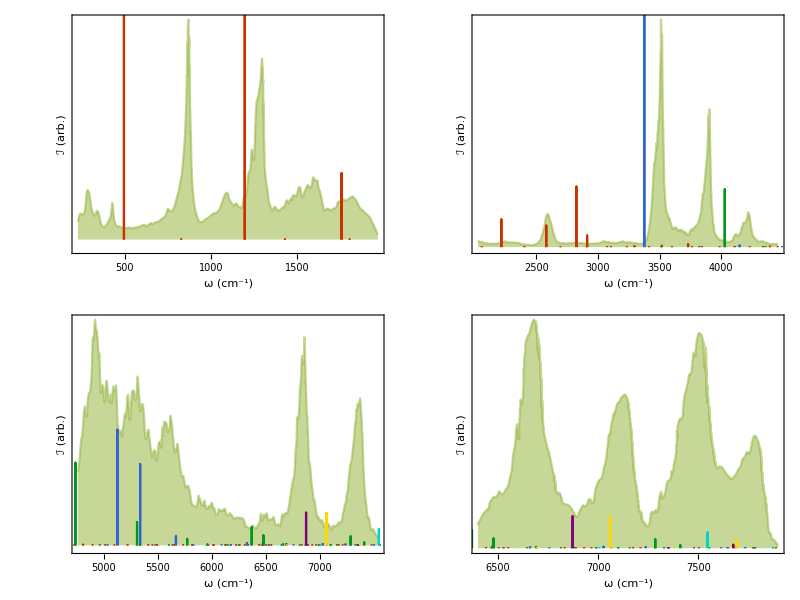

```mathematica
noCupGrid=makeCompPlot[
h5SpecParts[[{1, 5, 6, 7, 8, 9}]],
spectra
][[1, 2;;]]//Partition[#,2]&//Grid
```

```mathematica
expFig["norm_grid_no_cup",Pane[ noCupGrid, {600, Automatic}, ImageSizeAction->"ShrinkToFit"]]
```

/Users/Mark/Documents/UW/Research/H5+/figures/norm_grid_no_cup.pdf

##### H5Parallel

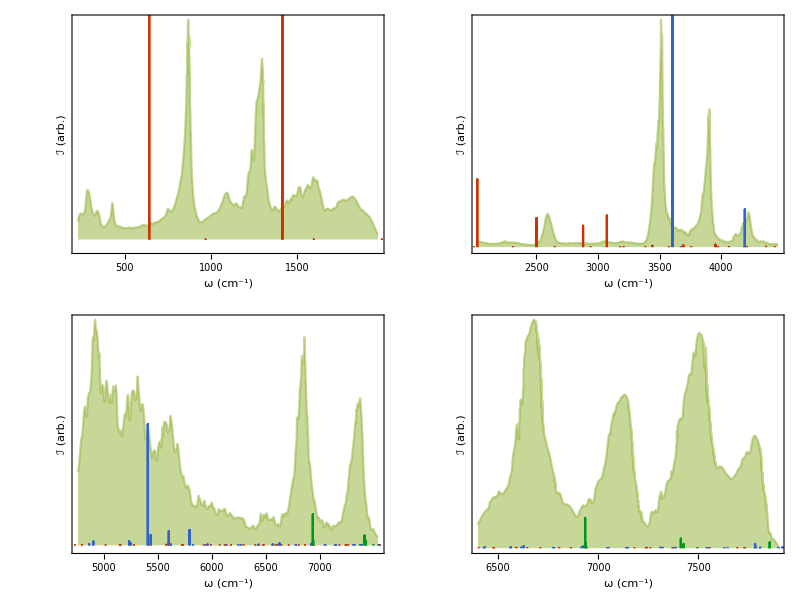

```mathematica
parallelGrid=
Partition[
makeCompPlot[
h5ParallelSpecParts[[;;3]],
spectra
][[1, 2;;]],
2
]//Grid
```

```mathematica
expFig["par_grid", Pane[parallelGrid, {600, Automatic}, ImageSizeAction->"ShrinkToFit"]]
```

/Users/Mark/Documents/UW/Research/H5+/figures/par_grid.pdf

No Coupling

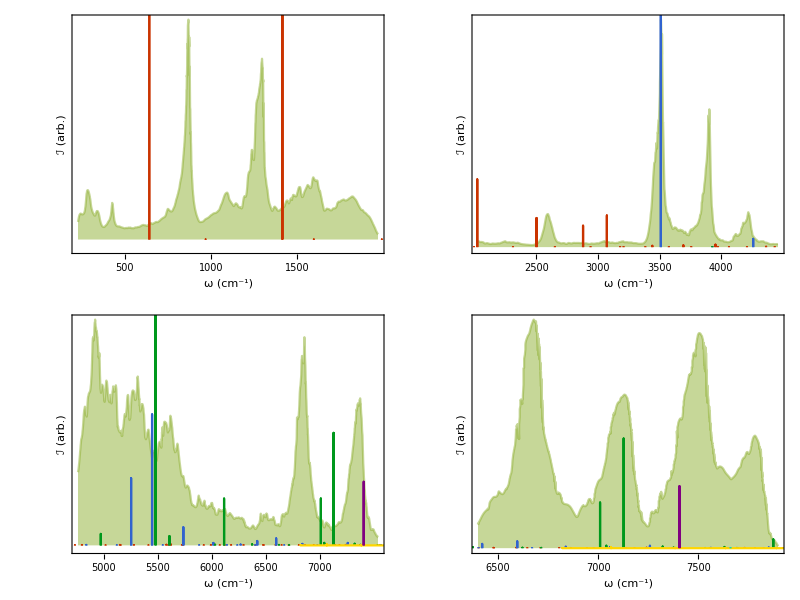

```mathematica
parallelGridNoCup=
Partition[
makeCompPlot[
h5ParallelSpecParts[[{1,5, 6, 7, 8, 9} ]],
spectra
][[1, 2;;]],
2
]//Grid
```

```mathematica
expFig["par_grid_no_cup", Pane[parallelGridNoCup, {600, Automatic}, ImageSizeAction->"ShrinkToFit"]]
```

/Users/Mark/Documents/UW/Research/H5+/figures/par_grid_no_cup.pdf

##### D5

```mathematica
makeCompPlot[
d5OldSpecParts[[;;3]],
{d5Expt}
]
```

```mathematica
makeCompPlot[
Drop[d5SpecParts, {2, 4}][[;;7]],
{d5Expt}
]
```

```mathematica
expFig["shitty_d5", shittyD5]
```

/Users/Mark/Documents/UW/Research/H5+/figures/shitty_d5.pdf

##### D5Parallel

```mathematica
makeCompPlot[
Join[
d5SpecParts[[;;3]],
d5ParallelSpecParts[[;;3]]
],
{d5Expt}
]
```

```mathematica
makeCompPlot[
Drop[d5SpecParts, {2, 4}][[;;7]],
{d5Expt}
]
```

```mathematica
expFig["shitty_d5", shittyD5]
```

/Users/Mark/Documents/UW/Research/H5+/figures/shitty_d5.pdf

## Wavefunctions

```mathematica
wfns=Import["/Users/Mark/Documents/UW/Research/H5+/results/H5OldOriginal/$Wavefunctions.mx"];
```

```mathematica
pullProj[wfns_, grid_, states_]:=
	With[{g2=grid, g=Min[grid["Points"]], len = Dimensions[grid][[1]], couplings=states},
		MapThread[
			Function[
				WavefunctionsObject[
					{
						#["Energies"],
						GridFunctionObject[
							g2,
							#@"Values"
							]&/@#["Wavefunctions"]
						},
					g2
					]&@wfns[[All, #;;#2]]
				],
			{
				1+Range[0, Length[couplings]-1]*len,
				Range[Length@couplings]*len
				}
			]
		]
```

```mathematica
proj2=pullProj[wfns[[2]], wfns[[1]]["Grid"], {2, 3}];
```

```mathematica
proj3=pullProj[wfns[[3]], wfns[[1]]["Grid"], {4, 5, 6}];
```

```mathematica
makeProjGrid//Clear;
makeProjGrid[proj_, n_:25, m_:5]:=
  Partition[
    Grid[{#}]&/@Transpose@
      Table[
        Show[
          ReplaceAll[
            ReplacePart[#,
              {1, 1, 1}->Map[If[#[[1]]>2.5, #-{1.8, 0}, #]&, #[[1, 1, 1]]]
              ]&[
              DeleteCases[#,{___, _GrayLevel, ___},Infinity]
              ],
           {l___, r_?ColorQ, e___}:>
  If[#[[3]]>#[[1]]&@ColorConvert[r, RGBColor],
              {
                l,
                r,
                EdgeForm@Directive[Gray, Thin],
                e
                },
              {l, r, e}
              ]
            ],
          PlotRange->{{-1.5,1.5},{1.2,2.8}},
          AspectRatio->Automatic
          ]&/@
        plotWfs[wfs[[;;n]], -.25, .25, 20,
          ColorFunction->"LakeColors"
          ],
        {wfs, proj}
        ],
    m
    ]//Grid[Transpose@#, Dividers->{{None, {GrayLevel[.95]}, None}, {None, {GrayLevel[.8]}, None}}]&
```

```mathematica
wfGrid1=makeProjGrid[{wfns[[1]]}, 24, UpTo[4]];
```

```mathematica
Export[localFig["wfGrid1.pdf"], wfGrid1];
```

```mathematica
wfGrid2=makeProjGrid[proj2, 24, UpTo[4]];
```

```mathematica
wf2Pos={1, 4, 5, 8, 9, 12, 13, 15, 18, 19, 21, 24};
contribs2=
Round[
Transpose[{
Diagonal[proj2[[1]]@"Overlaps"[proj2[[1]]]],
Diagonal[proj2[[2]]@"Overlaps"[proj2[[2]]]]
}],
.01
][[wf2Pos]];
states2=
{
{"ν_0", "ν_1"},
{"ν_0+ν_2?", "ν_1"},
{"ν_2", "ν_1"},
{"ν_4", "ν_3"},
{"ν_4", "ν_3"},
{"ν_6^*", "ν_5"},
{"ν_s", "ν_5"},
{"ν_6", "ν_5"},
{"ν_8", "ν_7^*"},
{"ν_(8^*)", "ν_7"},
{"ν_10", "ν_(9^*)"},
{"ν_10^*", "ν_9"}
};
```

```mathematica
trap=
Transpose@{
h5OldSpecParts[[2]]["Frequencies"][[wf2Pos]],
h5OldSpecParts[[2]]["Intensities"][[wf2Pos]],
MapThread[
Insert[#, Row[#, " "]&/@Transpose[{#2, #3}],{1, 2}]&,
{
Flatten[wfGrid2[[1]]][[wf2Pos]],
contribs2,
states2
}
]
};
```

```mathematica
Export[
localFig["wfGrid2Assigned.pdf"],
figStyleText@
Grid[
Prepend[#,{"Freq.", "ℐ", #2}], 
Alignment->Left,
Dividers->{
{None, {GrayLevel[.8]}, None},
{None, Black}
}
]&[trap, "1, 0 - 0, 1 / 1, 0 + 0, 1"]
];
```

```mathematica
Export[
localFig["wfGrid2Intense.pdf"],
ReplacePart[
wfGrid2,
{
1->
Partition[Flatten[wfGrid2[[1]]][[wf2Pos]], 3]
}
]
];
```

```mathematica
Export[
localFig["grid2Coeffs.pdf"],
figStyleText[
TableForm[
Flatten/@
Partition[
Round[
Transpose[{
Diagonal[proj2[[1]]@"Overlaps"[proj2[[1]]]],
Diagonal[proj2[[2]]@"Overlaps"[proj2[[2]]]]
}],
.01
][[;;24]],
4
],
TableHeadings->{{}, Flatten@ConstantArray[{"c_1", "c_2"}, 4]}
]
]
];
```

```mathematica
Export[
localFig["grid3Coeffs.pdf"],
figStyleText[
TableForm[
Flatten/@
Partition[
Round[
Transpose[{
Diagonal[proj3[[1]]@"Overlaps"[proj3[[1]]]],
Diagonal[proj3[[2]]@"Overlaps"[proj3[[2]]]],
Diagonal[proj3[[3]]@"Overlaps"[proj3[[3]]]]
}],
.01
][[;;24]],
4
],
TableHeadings->{{}, Flatten@ConstantArray[{"c_1", "c_2", "c3"}, 10]}
]
]
];
```

```mathematica
Export[localFig["wfGrid2.pdf"], wfGrid2, "AllowRasterization"->True]//SystemOpen
```

```mathematica
MapIndexed[
Export[localFig["wfGrid2_``.pdf"~TemplateApply~#2[[1]]], 
ReplacePart[
wfGrid2,
1->wfGrid2[[1, All, #]]
], 
"AllowRasterization"->True
]&,
{
{1, 2},
{3, 4, 5}
}
];
```

```mathematica
wfGrid3=makeProjGrid[proj3, 24, UpTo[4]];
```

```mathematica
wf3Pos={2, 4, 6, 8, 10};
```

```mathematica
wf3Pos={2, 4, 6, 8, 10};
contribs3=
Round[
Transpose[{
Diagonal[proj3[[1]]@"Overlaps"[proj3[[1]]]],
Diagonal[proj3[[2]]@"Overlaps"[proj3[[2]]]],
Diagonal[proj3[[3]]@"Overlaps"[proj3[[3]]]]
}],
.01
][[wf3Pos]];
states3=
{
{"ν_1","ν_0", "ν_1"},
{"ν_1","ν_0", "ν_1"},
{"ν_3","ν_2^*", "ν_1"},
{"ν_3","ν_2", "ν_1"},
{"ν_5^*","ν_2^*", "ν_3"}
};
```

```mathematica
trap3=
Transpose@{
h5OldSpecParts[[3]]["Frequencies"][[wf3Pos]],
h5OldSpecParts[[3]]["Intensities"][[wf3Pos]],
MapThread[
Insert[#, Row[#, " "]&/@Transpose[{#2, #3}],{1, 2}]&,
{
Flatten[wfGrid3[[1]]][[wf3Pos]],
contribs3,
states3
}
]
};
```

```mathematica
Export[
localFig["wfGrid3Assigned.pdf"],
figStyleText@
Grid[
Prepend[#,{"Freq.", "ℐ", #2}], 
Alignment->Left,
Dividers->{
{None, {GrayLevel[.8]}, None},
{None, Black}
}
]&[trap3,  "2, 0 / 1, 1 /0, 2"]
];
```

```mathematica
Export[
localFig["wfGrid3Intense.pdf"],
ReplacePart[
wfGrid3,
{
1->
Partition[Flatten[wfGrid3[[1]]][[wf3Pos]], UpTo[2]]
}
]
];
```

```mathematica
Export[localFig["wfGrid3.pdf"], wfGrid3, "AllowRasterization"->True]//SystemOpen
```

```mathematica
MapIndexed[
Export[localFig["wfGrid3_``.pdf"~TemplateApply~#2[[1]]], 
ReplacePart[
wfGrid3,
1->wfGrid3[[1, All, #]]
], 
"AllowRasterization"->True
]&,
{
{1, 2},
{3, 4, 5}
}
];
```

```mathematica
test2=
DeleteCases[$Failed]@Import["/Users/Mark/Documents/UW/Research/H5+/results/H5OldOriginal/r1r2Wavefunctions.mx"];
```

```mathematica
k=Nearest[Keys@test2, {0., 1.5}][[1]];
```

```mathematica
test2[k][[{4 ,5, 6}]]@"Plot"["PlotMode"->"Density", "PlotDisplayMode"->"List"]
```

```mathematica
test2[[2]][[{4 ,5, 6}]]@"Plot"["PlotMode"->"Density", "PlotDisplayMode"->"List"]
```

```mathematica
test2[[-1]][[{4 ,5, 6}]]@"Plot"["PlotMode"->"Density", "PlotDisplayMode"->"List"]
```

#### H5HighRes

```mathematica
h5Wfns=Import["/Users/Mark/Documents/UW/Research/H5+/results/H5HighRes/Wavefunctions.mx"];
```

```mathematica
h5Wfns["OneQuantum"][[;;3]]@"Plot"["PlotMode"->"Density",
AspectRatio->1/2, 
ImageSize->{Automatic, 350}
]
```

```mathematica
h5Wfns["TwoQuanta"][[;;3]]@"Plot"[
BoxRatios->{3, 1, 1}, 
ImageSize->{Automatic, 350}
]
```

### H5Parallel Messed Up

```mathematica
wtf=Import["~/Desktop/r1r2Wavefunctions.mx"];
```

```mathematica
wtf//Keys
```

```mathematica
fuckers=wtf//DeleteCases[$Failed];
```

```mathematica
fuckers//Length
```

3960

```mathematica
fuckers[[800]]@"Grid"//CoordinateBounds
```

{{0.27247,0.976726},{0.27247,0.976726}}

```mathematica
fuckers[[800]][[;;3]]@"Plot"[]
```

```mathematica
Import["/Users/Mark/Documents/UW/Research/H5+/results/D5Old/extrap$39936208.mx"]//ListPlot3D
```